# Improved Ambient Occlusion

We can write the “direct” irradiance estimate as:
	E_0(x)=∫_Ω^□ L_0 V_dir(ω_i)(n.ω_i)ⅆ ω_i
Where L_0 is the radiance value perceived from the (distant) environment and V_dir(ω_i) represents the direct visibility function that equals 1 if the ray is unoccluded by the surface, 0 otherwise.

We can then write the general expression for the “indirect” irradiance estimate as:
	E_(n+1)(x)=∫_Ω^□ L_i(x,ω_i )V_ind(ω_i)(n.ω_i)ⅆ ω_i
Where V_ind(ω_i) represents the indirect visibility function that equals 1 if the ray is occluded by the surface, 0 otherwise (so V_ind(ω_i)=1-V_dir(ω_i) ).

We can rewrite the perceived incoming luminance L_i(x,ω_i ) from a neighbor location x' as:
	L_i(x,ω_i )=(ρ(x'))/π E_n(x')
And finally:
	E_(n+1)(x)=∫_Ω^□ (ρ(x'))/π E_n(x')V_ind(ω_i)(n.ω_i)ⅆ ω_i

We easily see that, assuming a constant reflectance everywhere so (ρ(x'))/π=(ρ(x))/π=ρ/π, we can compute each bounce of the irradiance incrementally by re-using the previous irradiance at the indirect neighbor locations since:
	E_(n+1)(x)=ρ/π∫_Ω^□ E_n(x')V_ind(ω_i)(n.ω_i)ⅆ ω_i

## Fitting Experimental Data

After writing the program that computes the AO and the multiple indirect bounces from a height map, we collect the bounced illuminance values into histograms where the bin indices are given by the AO values: this bascially computes the average indirect illuminance perceived by a point given its AO value (AO value is in [0,2π] but we rescaled it to [0,1] for energy conservation purposes).
We do that for multiple bounces to try and find a pattern in the shape and amplitude of the curves...

To generate the curves shown below, we used the WallHeight.png as a height map, and its corresponding WallNormal.png as a normal map.
We also chose a height value of 10 cm for a total wall length of 1 meter, 1024 rays at 179° cone aperture.
It gave some nice curves without the annoying artefacts found at the extremas that can be found with other maps.

```mathematica
ClearAll["Global`*"]
```

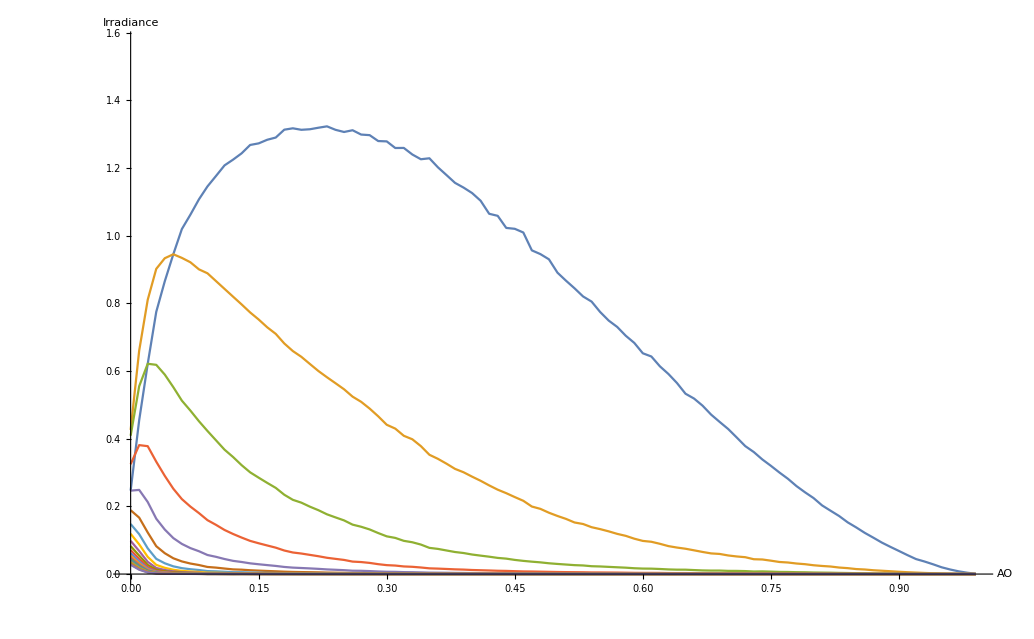

```mathematica
SetDirectory[NotebookDirectory[]]; 
tableSize = 100;
bouncesCount = 20;
rawArray=Table[ BinaryReadList["WallHeight"<>ToString[i]<>".float", "Real32"],{i,1,bouncesCount}];
bounces = Table[Table[{(i-1)/tableSize,rawArray[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];
ListLinePlot[bounces,PlotRange->{0,π/2},AxesLabel->{"AO","Irradiance"}]
```

Here we show the influence on the maximum height encoded by the height map on the resulting histogram curves: we see that apart from a slight compression to the left on bounce indices > 1, they are basically identical.
We notice a small discrepancy in the 5 cm curve and assume it will get worse when the height amplitudes continue to decrease, eventually becoming totally flat so no bounce can occur at all.
We can imagine the smae phenomenon occurs when the height map amplitudes become very large so no direct light can even reach the bottom of the surface.
Anyway, we will focus on the “normal regime” by assuming a height amplitude equal to 1/10 the size of the height map.
The height map we used is noisy enough (a brick wall texture with many details) to be considered a general  case from which all other cases derive.

```mathematica
(*bounces5cm = Table[Table[{(i-1)/tableSize,rawArray[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];*)
(*bounces15cm = Table[Table[{(i-1)/tableSize,rawArray[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];*)
(*bounces25cm = Table[Table[{(i-1)/tableSize,rawArray[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];*)
Manipulate[Show[
ListLinePlot[bounces[[bounceIndex]],PlotRange->{0,π/2}],
ListLinePlot[bounces5cm[[bounceIndex]],PlotRange->Full,PlotStyle->Red],
ListLinePlot[bounces15cm[[bounceIndex]],PlotRange->Full,PlotStyle->Green],
ListLinePlot[bounces25cm[[bounceIndex]],PlotRange->Full,PlotStyle->Blue]
],{bounceIndex,1,bouncesCount,1}]
```

These were the original curves where I made the mistake of using initial direct illuminance E0 instead of AO to drive the histogram bins storage:

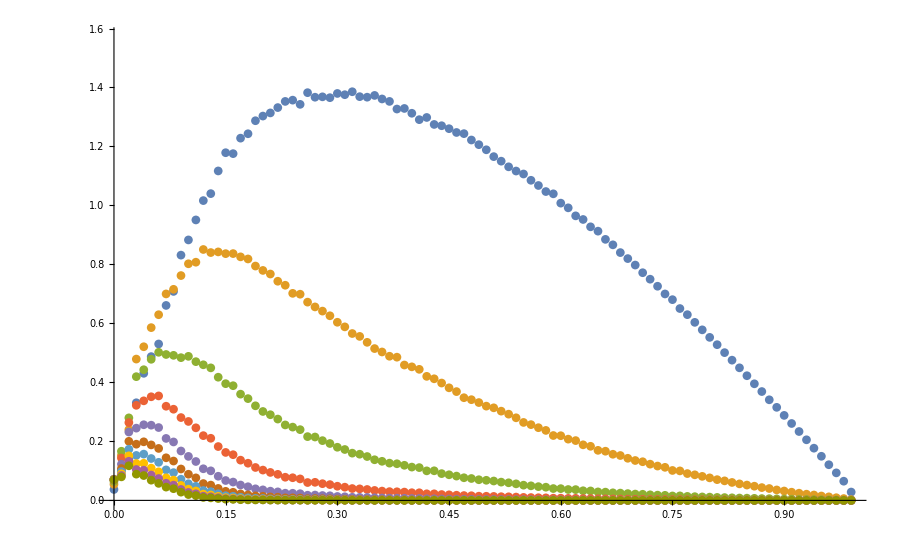

## Fitting the Difference between Actual Direct Irradiance and AO Simplification

Showing the irradiance received directly, without any bounce, as a function of AO:

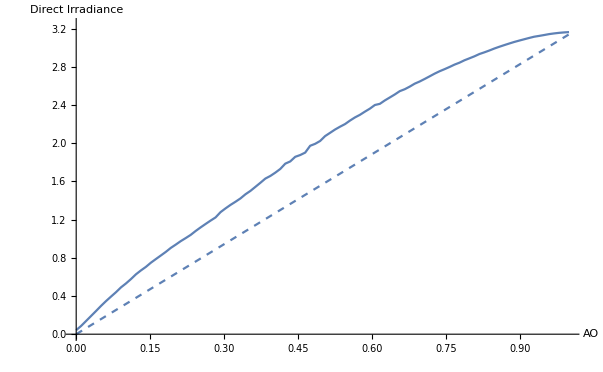

```mathematica
rawArray0=BinaryReadList["WallHeight0.float", "Real32"];
E0 = Table[{(i-1)/(tableSize-1),rawArray0[[i]]},{i,1,tableSize}];
Show[ListLinePlot[E0,PlotRange->{{0,1},{0,π+0.1}},AxesLabel->{"AO","Direct Irradiance"}],Plot[π*x,{x,0,1},PlotStyle->Dashed]]
```

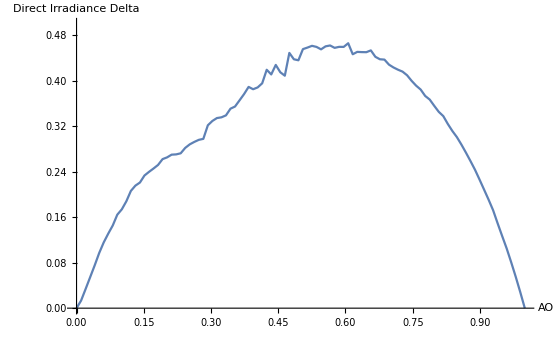

```mathematica
flatE0 = Table[{(i-1)/(tableSize-1),rawArray0[[i]]-(i-1)/(tableSize-1)*(rawArray0[[tableSize]]-rawArray0[[1]]) - rawArray0[[1]]},{i,1,tableSize}];
ListLinePlot[flatE0,PlotRange->{0,0.5},AxesLabel->{"AO","Direct Irradiance Delta"}]
```

{a→-0.00133309,b→1.3964,c→0.397396}

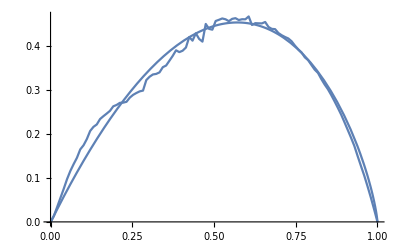

```mathematica
Clear[a,b,c,x,modelEO,fitEO];
modelE0=a * x^b*(1-x)^c;
modelE0=a+1.5 * x^1*(1-x)^0.75;
fitE0=FindFit[flatE0,{modelE0,b >0,c>0},{a,{b,1},c},{x}]
Show[
ListLinePlot[flatE0,PlotRange->Full],
Plot[modelE0/.fitE0,{x,0,1}]
]
```

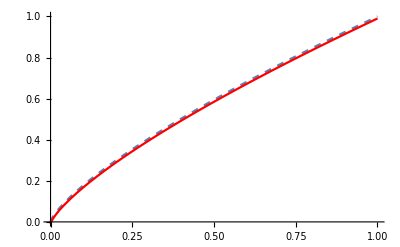

```mathematica
Show[
Plot[x^0.75,{x,0,1},PlotStyle->Dashed],
Plot[x/(√(√x))-0.01,{x,0,1},PlotStyle->Red]
]
```

x+0.5 (1-x)^(3/4) x

(1+0.5 (1-x)^(3/4)) x

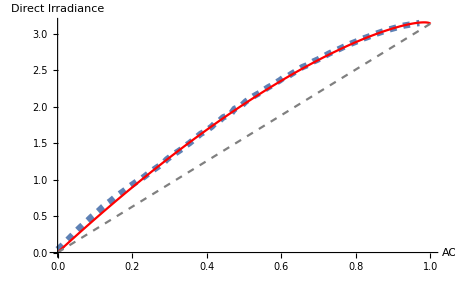

```mathematica
G[x_]=x+0.5*x*(1-x)/(√(√(1-x)))
G[x_]=x*(1+0.5*(1-x)/(√(√(1-x))))
Show[
ListLinePlot[E0,PlotRange->{0,0.01+π},PlotStyle->{Dashed,Thickness->0.01},AxesLabel->{"AO","Direct Irradiance"}],
Plot[π*G[x],{x,0,1},PlotStyle->Red],
Plot[π*x,{x,0,1},PlotStyle->{Dashed,Gray}]
]
```

## Summing the Curves

These curves represent

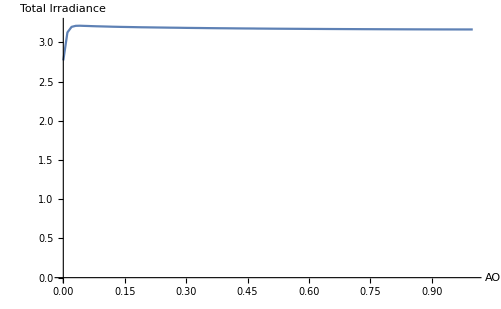

```mathematica
ρ=1.0;
sumBounces=Table[{(i-1)/(tableSize-1),E0[[i]][[2]]+ Sum[ρ^j*bounces[[j]][[i]][[2]],{j,1,bouncesCount}]},{i,1,tableSize}];

ListLinePlot[sumBounces,PlotRange->{0,0.1+π},AxesLabel->{"AO","Total Irradiance"}]
```

```mathematica
Manipulate[
(*sumTable=ρ*bounces[[1]]+ρ^2*bounces[[2]]+ρ^3*bounces[[3]]+(ρ/π)^4*bounces[[4]]+ρ^5*bounces[[5]]+ρ^6*bounces[[6]]+ρ^7*bounces[[7]];
sumTable=Sum[(ρ/1)^i*bounces[[i]],{i,1,bouncesCount}];*)
finalTable0=Table[{(i-1)/(tableSize-1),E0[[i]][[2]]+ Sum[ρ^j*bounces[[j]][[i]][[2]],{j,1,bouncesCount}]},{i,1,tableSize}];
finalTable1=Table[{(i-1)/(tableSize-1),π*G[(i-1)/(tableSize-1)]+ Sum[ρ^j*bounces[[j]][[i]][[2]],{j,1,bouncesCount}]},{i,1,tableSize}];
Show[
ListLinePlot[finalTable0,PlotRange->{0,0.1+π}],
ListLinePlot[finalTable1,PlotRange->{0,0.1+π},PlotStyle->Dashed]]
,{{ρ,1},0,1}
]
```

## Starting the Fitting

Intuitively, it looks like a log-normal distribution curve that we can model as f(x)=a*x*(1-x)*e^-bx.
We can see below that it’s actually a very nice fit for the curves and may even deduce a general rule to find a and b coefficients as a function of the bounce index...

```mathematica
Manipulate[Plot[8*x*(1-x)*ⅇ^(-k*x),{x,0,1},PlotRange->{0,π/2}],{{k,1},0,20}]
```

```mathematica
Clear[a,b]
model=b/a*x*(1-x)*Exp[-b*x];
fitter[i_]:=Module[{},
FindFit[bounces[[i]], model,{a,{b,20}},{x}]
]
fits=Table[fitter[bounceIndex],{bounceIndex,1,bouncesCount}]
```

## Runtime Use of the AO value

For runtime use, we (incorrectly!) simplify the integral for directly-perceived illuminance ∫L(x,ω_i) V(x,ω_i) cosθ sinθⅆθ ≈[∫L(x,ω_i) cosθ sinθⅆθ]  [∫V(x,ω_i)  sinθⅆθ] = E(x,n) . AO
The integration of the constant visibility term for a flat, unoccluded surface equals 2π, so we need to apply a 1/(2π)factor to obtain the classical AO term we find in a AO texture.
So let’s decide that an AO map’s value should be multiplied by the irradiance perceived by the surface to obtain a [0,π] value that we later scale by the surface’s albedo ρ/π to finally obtain the reflected radiance in the range [0,1] in the outgoing direction ω_o:
	L(x,ω_o) = ρ/π AO E(x)

Symbolic integration of the cosine-weighted constant luminance L(x,ω_i)=1 function ∫L(x,ω_i)cosθ sinθⅆθ=∫cosθ sinθⅆθ= -1/2 cos^2 θ
Integration over the entire hemisphere ∫_0^(2π) ∫_0^(π/2) cosθ sinθⅆθⅆϕ=π

```mathematica
2π * Integrate[Cos[θ]Sin[θ],{θ,0,π/2}]
2π * Integrate[Sin[θ],{θ,0,π/2}]
```

π

2 π